# Équations différentielles de oscillateur harmonique

## Initiation

### Équation différentielle

```mathematica
equation=u''[x]+n^2 u[x]==0;
```

Avec les frontières :

```mathematica
a=0;b=2π;
```

Et les conditions frontières suivantes :

α_1 u(a)+(β_1 d/dx u(x)|)_(x=a)=0
α_2 u(b)+(β_2 d/dx u(x)|)_(x=b)=0

### Les Calcules

#### Équation

```mathematica
Subscript[p, 2][x]=Coefficient[equation[[1]],u''[x],1];
```

```mathematica
Subscript[p, 1][x]=Coefficient[equation[[1]],u'[x],1];
```

```mathematica
Subscript[p, 0][x]=Coefficient[equation[[1]],u[x],1]-Coefficient[Coefficient[equation[[1]],u[x],1],x,0];
```

```mathematica
λ=Coefficient[Coefficient[equation[[1]],u[x],1],x,0];
```

```mathematica
Polynomes=Grid[{{"p_2[x]=",Subscript[p, 2][x]},{"p_1[x]=",Subscript[p, 1][x]},{"p_0[x]=",Subscript[p, 0][x]},{"    λ=",λ}},Alignment->Left];
```

```mathematica
t1= {"Équation :   ",Subscript[p, 2][x]HoldForm[d^2/dx^2] HoldForm[ u[x]]+Subscript[p, 1][x] HoldForm[d/dx] HoldForm[ u[x]]+Subscript[p, 0][x]  HoldForm[ u[x]]+λ HoldForm[u[x]]==0};
```

```mathematica
t2={"Les coéficients :   ",Polynomes};
```

```mathematica
Equ=Grid[{t1,t2},Alignment->Left];
```

```mathematica
L=Subscript[p, 2][x]u''[x]+Subscript[p, 1][x] u'[x]+Subscript[p, 0][x] u[x];
```

```mathematica
t3={"Avec l'opérateur L :  ",Subscript[p, 2][x]HoldForm[d^2/dx^2] +Subscript[p, 1][x] HoldForm[d/dx] +Subscript[p, 0][x] };
```

```mathematica
t4= {"On peut écrire : ",HoldForm[L u[x]]+λ HoldForm[u[x]]==0 };
```

```mathematica
OEqu=Grid[{t1,t3,t4},Alignment->Left];
```

```mathematica
t={"________________________________________________________________"};
```

#### Équation Adjoint

```mathematica
Adjoint=D[(Subscript[p, 2][x]D[u[x], x]), x]-Subscript[p, 0][x]u[x]+ λ u[x]==0;
```

```mathematica
L̄=D[(Subscript[p, 2][x]D[u[x], x]), x]-Subscript[p, 0][x]u[x];
```

```mathematica
t1={"Équation Adjoint :  ",(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] HoldForm[ u[x]]]-Subscript[p, 0][x] HoldForm[u[x]]+λ HoldForm[u[x]]==0};
```

```mathematica
t2={"Équation est auto - adjoint ?  ",If[Simplify[equation]===Simplify[Adjoint],"Équation Adjoint≡Équation ⟹ Oui","Équation Adjoint≢Équation ⟹ Non"]};
```

```mathematica
EquAdj=Grid[{t1,t2},Alignment->Left];
```

```mathematica
t3={"Avec l'opérateur L̄ :  " ,(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] ]-Subscript[p, 0][x]  };
```

```mathematica
t4={"On peut écrire : ",HoldForm[L̄ u[x]]+λ HoldForm[u[x]]==0 };
```

```mathematica
t5={"Opérateur est auto - adjoint ?  ",If[Simplify[L̄]===Simplify[L],"L̄ ≡ L ⟹ Oui","L̄ ≢ L ⟹ Non"]};
```

```mathematica
OEquAdj=Grid[{t1,t3,t4,t5},Alignment->Left];
```

#### Équation × w[x]

```mathematica
w[x]=Exp[∫(Subscript[p, 1][x]-D[Subscript[p, 2][x],x])/(Subscript[p, 2][x])ⅆx];
```

```mathematica
equation=Subscript[p, 2][x] w[x]u''[x]+Subscript[p, 1][x]w[x] u'[x]+Subscript[p, 0][x]w[x]u[x]+λ w[x]u[x]==0
```

n^2 u[x]+u''[x]==0

```mathematica
Subscript[p, 2][x]=Coefficient[equation[[1]],u''[x],1];
```

```mathematica
Subscript[p, 1][x]=Coefficient[equation[[1]],u'[x],1];
```

```mathematica
Subscript[p, 0][x]=Coefficient[equation[[1]],u[x],1]-Coefficient[Coefficient[equation[[1]],u[x],1],x,0];
```

```mathematica
Polynomes=Grid[{{"p_2[x]=",Subscript[p, 2][x]},{"p_1[x]=",Subscript[p, 1][x]},{"p_0[x]=",Subscript[p, 0][x]},{"    λ=",λ}},Alignment->Left];
```

```mathematica
t1={"w[x] :  ",w[x]};
```

```mathematica
t2= {"w[x] × Équation :   ",Subscript[p, 2][x]HoldForm[d^2/dx^2] HoldForm[ u[x]]+Subscript[p, 1][x] HoldForm[d/dx] HoldForm[ u[x]]+Subscript[p, 0][x]  HoldForm[ u[x]]+λ w[x]HoldForm[u[x]]==0};
```

```mathematica
t3={"Les coéficients :   ",Polynomes};
```

```mathematica
WEqua=Grid[{t1,t2,t3},Alignment->Left];
```

```mathematica
t4={"Avec l'opérateur ℒ :  " ,(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] ]-Subscript[p, 0][x]  };
```

```mathematica
t5={"On peut écrire : ",HoldForm[ℒ u[x]]+λ w[x]HoldForm[u[x]]==0 };
```

```mathematica
OWEqua=Grid[{t1,t2,t4,t5},Alignment->Left];
```

#### Équation × w[x] Adjoint

```mathematica
Adjoint=D[(Subscript[p, 2][x]D[u[x], x]), x]-Subscript[p, 0][x]u[x]+ λ w[x]u[x]==0
```

n^2 u[x]+u''[x]==0

```mathematica
ℒ=Subscript[p, 2][x]u''[x]+Subscript[p, 1][x] u'[x]+Subscript[p, 0][x] u[x];
```

```mathematica
Polynomes=Grid[{{"p_2[x]=",Subscript[p, 2][x]},{"p_1[x]=",Subscript[p, 1][x]},{"p_0[x]=",Subscript[p, 0][x]},{"    λ=",λ}},Alignment->Left];
```

```mathematica
t1={"w[x] × Équation Adjoint :  ",(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] HoldForm[ u[x]]]-Subscript[p, 0][x]HoldForm[u[x]]+λ w[x] HoldForm[u[x]]==0};
```

```mathematica
t2={"Équation est auto - adjoint ?  ",If[Simplify[equation]===Simplify[Adjoint],"Équation Adjoint≡Équation ⟹ Oui","Équation Adjoint≢Équation ⟹ Non"]};
```

```mathematica
t3={"Les coéficients :   ",Polynomes};
```

```mathematica
WEquaAdj=Grid[{t1,t2,t3},Alignment->Left];
```

```mathematica
ℒ̄=D[(Subscript[p, 2][x]D[u[x], x]), x]-Subscript[p, 0][x]u[x];
```

```mathematica
t4={"Avec l'opérateur ℒ̄ :  " ,(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] ]-Subscript[p, 0][x]  };
```

```mathematica
t5={"On peut écrire : ",HoldForm[ℒ̄ u[x]]+λ HoldForm[u[x]]==0 };
```

```mathematica
t6={"Opérateur est auto - adjoint ?  ",If[Simplify[ℒ̄]===Simplify[ℒ],"ℒ̄ ≡ ℒ ⟹ Oui","ℒ̄ ≢ ℒ ⟹ Non"]};
```

```mathematica
OWEquaAdj=Grid[{t1,t4,t5,t6},Alignment->Left];
```

#### Équation S-L

```mathematica
t1={"Équation Sturm-Liouville :  ",(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] HoldForm[ u[x]]]-Subscript[p, 0][x]HoldForm[u[x]]+λ w[x] HoldForm[u[x]]==0};
```

```mathematica
PolynomesSL=Grid[{{"p[x]=",Subscript[p, 2][x]w[x]},{"q[x]=",-Subscript[p, 0][x]w[x]},{"   λ=",λ}},Alignment->Left];
```

```mathematica
t2={"Avec les frontières : ",Grid[{{"a =",a},{"b =",b}},Alignment->Left]};
```

```mathematica
t3={"w[x] :  ",w[x]};
```

```mathematica
t4={"Les coéficients :   ",PolynomesSL};
```

```mathematica
EquSL=Grid[{t1,t2,t3,t4},Alignment->Left];
```

```mathematica
t5={"Avec l'opérateur ℒ :  " ,(d/dx)[Subscript[p, 2][x]HoldForm[d/dx] ]-Subscript[p, 0][x]  };
```

```mathematica
t6={"On peut écrire : ",HoldForm[ℒ u[x]]+λ w[x]HoldForm[u[x]]==0 };
```

```mathematica
OEquSL=Grid[{t1,t2,t3,t4,t5,t6},Alignment->Left];
```

#### Res

```mathematica
Resultat1=Grid[{{Equ},t,{EquAdj},t,{WEqua},t,{WEquaAdj},t,{EquSL}},Alignment->Left,Frame-> True];
```

```mathematica
Resultat2=Grid[{{OEqu},t,{OEquAdj},t,{OWEqua},t,{OWEquaAdj},t,{OEquSL}},Alignment->Left,Frame-> True];
```

### En terme de l’équation différentielle

```mathematica
Resultat1
```

Équation :    | n^2 u[x]+d^2/dx^2 u[x]==0
Les coéficients :    | p_2[x]= | 1
p_1[x]= | 0
p_0[x]= | 0
    λ= | n^2
________________________________________________________________
Équation Adjoint :   | d/dx[d/dx u[x]]+n^2 u[x]==0
Équation est auto - adjoint ?   | Équation Adjoint≡Équation ⟹ Oui
________________________________________________________________
w[x] :   | 1
w[x] × Équation :    | n^2 u[x]+d^2/dx^2 u[x]==0
Les coéficients :    | p_2[x]= | 1
p_1[x]= | 0
p_0[x]= | 0
    λ= | n^2
________________________________________________________________
w[x] × Équation Adjoint :   | d/dx[d/dx u[x]]+n^2 u[x]==0
Équation est auto - adjoint ?   | Équation Adjoint≡Équation ⟹ Oui
Les coéficients :    | p_2[x]= | 1
p_1[x]= | 0
p_0[x]= | 0
    λ= | n^2
________________________________________________________________
Équation Sturm-Liouville :   | d/dx[d/dx u[x]]+n^2 u[x]==0
Avec les frontières :  | a = | 0
b = | 2 π
w[x] :   | 1
Les coéficients :    | p[x]= | 1
q[x]= | 0
   λ= | n^2

### En terme de l’opérateur différentielle

```mathematica
Resultat2
```

Équation :    | n^2 u[x]+d^2/dx^2 u[x]==0
Avec l'opérateur L :   | d^2/dx^2
On peut écrire :  | n^2 u[x]+L u[x]==0
________________________________________________________________
Équation Adjoint :   | d/dx[d/dx u[x]]+n^2 u[x]==0
Avec l'opérateur L̄ :   | d/dx[d/dx]
On peut écrire :  | n^2 u[x]+L̄ u[x]==0
Opérateur est auto - adjoint ?   | L̄ ≡ L ⟹ Oui
________________________________________________________________
w[x] :   | 1
w[x] × Équation :    | n^2 u[x]+d^2/dx^2 u[x]==0
Avec l'opérateur ℒ :   | d/dx[d/dx]
On peut écrire :  | n^2 u[x]+ℒ u[x]==0
________________________________________________________________
w[x] × Équation Adjoint :   | d/dx[d/dx u[x]]+n^2 u[x]==0
Avec l'opérateur ℒ̄ :   | d/dx[d/dx]
On peut écrire :  | n^2 u[x]+ℒ̄ u[x]==0
Opérateur est auto - adjoint ?   | ℒ̄ ≡ ℒ ⟹ Oui
________________________________________________________________
Équation Sturm-Liouville :   | d/dx[d/dx u[x]]+n^2 u[x]==0
Avec les frontières :  | a = | 0
b = | 2 π
w[x] :   | 1
Les coéficients :    | p[x]= | 1
q[x]= | 0
   λ= | n^2
Avec l'opérateur ℒ :   | d/dx[d/dx]
On peut écrire :  | n^2 u[x]+ℒ u[x]==0

## Opérateur ℒ est Hermitien

On va montrer que :

1 - Les valeures propres de l' opérateur Hermitien ℒ sont réelles.

2 - Les fonctions propres de l' opérateur Hermitien ℒ sont orthogonales, pondérées par w[x].

3 - Les fonctions propres de l’opérateur ℒ forment une base complète  sur laquelle on peut exprimer (développer) n’importe quelle fonction.

## Les limites

```mathematica
Subscript[n, min]=1;Subscript[n, max]=4;
```

```mathematica
Subscript[m, min]=1;Subscript[m, max]=4;
```

```mathematica
Subscript[x, min]=0;Subscript[x, max]=2π;
```

## Les valeures propres de l’opérateur Hermitien ℒ sont réelles.

```mathematica
Table[{n,λ},{n,Subscript[n, min],Subscript[n, max]}]//TableForm
```

1 | 1
2 | 4
3 | 9
4 | 16

#### Est ce que les valeurs propres de l’operateur ℒ sont réel ?

```mathematica
Table[λ,{n,Subscript[n, min],Subscript[n, max]}]*==Table[λ,{n,Subscript[n, min],Subscript[n, max]}]
```

True

## Les fonctions propres de l’opérateur Hermitien ℒ sont orthogonales, pondérées par w[x].

```mathematica
sol=DSolve[equation, u[x], x]
```

{{u[x]→C[1] Cos[n x]+C[2] Sin[n x]}}

```mathematica
Subscript[𝓊, n_][x_]:=Sin[n x]
```

```mathematica
Table[{n,Subscript[𝓊, n][x]},{n,Subscript[n, min],Subscript[n, max]}]//TableForm//TraditionalForm
```

1 | sin(x)
2 | sin(2 x)
3 | sin(3 x)
4 | sin(4 x)

### Est ce que les fonctions propres de l' operateur ℒ sont orthogonales?

```mathematica
TableForm[Table[∫_a^b w[x]Subscript[𝓊, m][x]Subscript[𝓊, n][x]ⅆx,{m,Subscript[m, min],Subscript[m, max]},{n,Subscript[n, min],Subscript[n, max]}]]
```

π | 0 | 0 | 0
0 | π | 0 | 0
0 | 0 | π | 0
0 | 0 | 0 | π

```mathematica
TableForm[Table[π KroneckerDelta[m,n],{m,Subscript[m, min],Subscript[m, max]},{n,Subscript[n, min],Subscript[n, max]}]]
```

π | 0 | 0 | 0
0 | π | 0 | 0
0 | 0 | π | 0
0 | 0 | 0 | π

### Représentation graphique

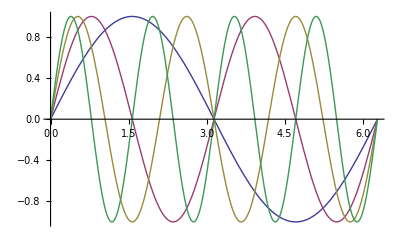

```mathematica
Plot[Evaluate[Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]],{x,Subscript[x, min],Subscript[x, max]}]
```

### On peut normaliser la base des fonctions propres de l’opérateur ℒ

```mathematica
Subscript[ϕ, n_][x_]:=(Subscript[𝓊, n][x])/(√(∫_a^b w[x]Subscript[𝓊, n][x]Subscript[𝓊, n][x]ⅆx))
```

```mathematica
Table[{n,Subscript[ϕ, n][x]},{n,Subscript[n, min],Subscript[n, max]}]//Simplify//TableForm
```

1 | Sin[x]/(√π)
2 | Sin[2 x]/(√π)
3 | Sin[3 x]/(√π)
4 | Sin[4 x]/(√π)

```mathematica
Table[∫_a^b w[x]Subscript[ϕ, m][x]Subscript[ϕ, n][x]ⅆx,{m,Subscript[m, min],Subscript[m, max]},{n,Subscript[n, min],Subscript[n, max]}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

### Représentation graphique

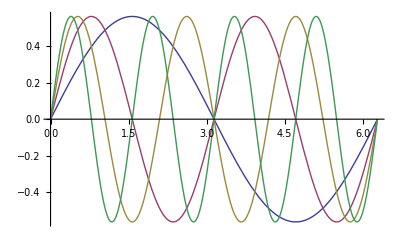

```mathematica
Plot[Evaluate[Table[Subscript[ϕ, n][x],{n,Subscript[n, min],Subscript[n, max]}]],{x,Subscript[x, min],Subscript[x, max]}]
```

## Les fonctions propres de l'opérateur Hermitien ℒ forment une base complète.

### Fonction normée à développer

```mathematica
Ψ[x_] = SquareWave[{-1, 1}, x/π]/(√(∫_a^b w[x] Abs[SquareWave[{-1, 1}, x/π]]^2 ⅆx))//Simplify
```

SquareWave[{-1,1},x/π]/(√(2 π))

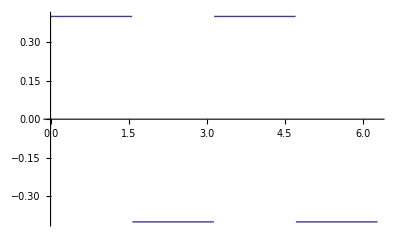

```mathematica
Plot[Evaluate[Ψ[x]],{x,Subscript[x, min],Subscript[x, max]}]
```

### Les coeficients de Fourier

```mathematica
Subscript[c, n_]:=∫_a^b w[x]Subscript[ϕ, n][x]Ψ[x] ⅆx
```

```mathematica
Table[{n,Subscript[c, n]},{n,Subscript[n, min],Subscript[n, max]}]//Simplify//TableForm
```

1 | 0
2 | (2 √2)/π
3 | 0
4 | 0

### Dévelopement de Ψ(x) sur la base orthonormale

```mathematica
No=10
```

10

```mathematica
∑_(i=1)^No Subscript[c, i] Subscript["ϕ", i][x]//Simplify
```

(2 √2 (15 ϕ_2[x]+5 ϕ_6[x]+3 ϕ_10[x]))/(15 π)

```mathematica
∑_(i=1)^No Subscript[c, i] Subscript[ϕ, i][x]//Simplify
```

(2 √2 (15 Sin[2 x]+5 Sin[6 x]+3 Sin[10 x]))/(15 π^(3/2))

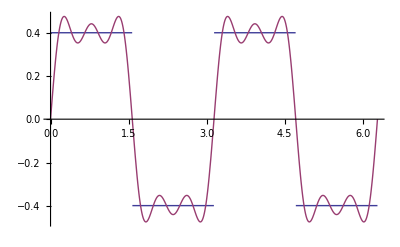

```mathematica
Plot[Evaluate[{Ψ[x],∑_(i=1)^No Subscript[c, i] Subscript[ϕ, i][x]}],{x,Subscript[x, min],Subscript[x, max]},PlotRange->All]
```